## A366637: Number of divisors of 7^n + 1.

### MATHEMATICA PROGRAM:

```mathematica
DivisorSigma[0,7^Range[0,62]+1]
```

{2,4,6,8,4,16,24,16,8,16,32,16,32,16,12,64,8,8,48,16,16,128,48,8,16,32,24,32,64,8,512,32,16,128,48,1024,256,16,12,256,64,64,96,512,32,2048,96,8,64,2048,640,128,32,64,384,3072,256,256,96,64,512,8,48}

### Formula:

a(n) = sigma0(7^n+1) = A000005(A034491(n)).

### Plot section:

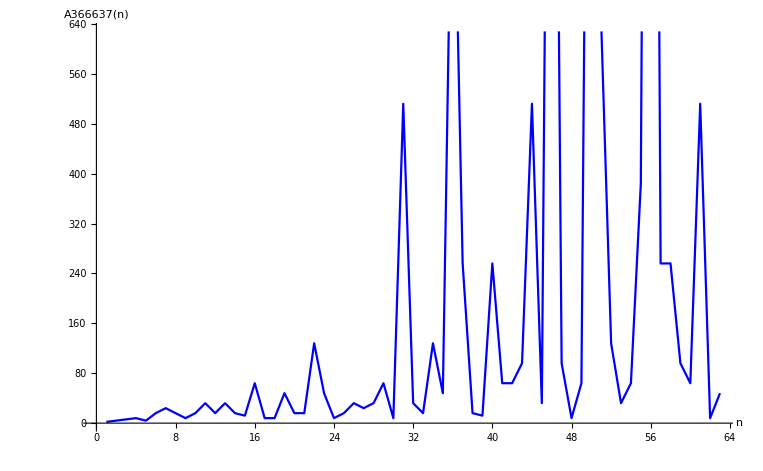

```mathematica
ListPlot[DivisorSigma[0, 7^Range[0,62] + 1], Joined->True, PlotStyle->Blue, AxesLabel->{"n", "A366637(n)"}, LabelStyle->Directive [Black, Bold]]
```

### References:

Sean A. Irvine, Number of divisors of 7^n+1., Entry A366637 in The On-Line Encyclopedia of Integer Sequences, https://oeis.org/A366637